-Graphics-

```mathematica
Integrate[Sin[x](1-(Cos[x])^2),{x,0,Pi}]
```

4/3

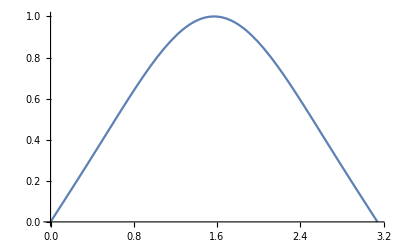
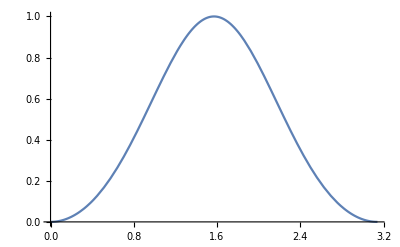

```mathematica
{Plot[Cos[π/2*Cos[θ]]/Sin[θ],{θ,0,π}],Plot[(Cos[π/2*Cos[θ]]/Sin[θ])^2,{θ,0,π}]}
```

```mathematica
MaxValue[Abs[Cos[π/2*Cos[θ]]/Sin[θ]],{θ}]
```

1

```mathematica
f[θ_]:=Cos[π/2*Cos[θ]]/Sin[θ]
```

```mathematica
D[Cos[π/2*Cos[θ]]/Sin[θ],θ]
```

-Cos[1/2 π Cos[θ]] Cot[θ] Csc[θ]+1/2 π Sin[1/2 π Cos[θ]]